.

```mathematica
sys2 := {D[Rp[t],t]==(k1 S (RT-Rp[t]))/(Km1 +RT-Rp[t])-(k2 Rp[t])/(Km2 +Rp[t])}(*pdes*)
```

```mathematica
parm = {k1->1, k2->1 , RT-> 1,Km1-> 0.05,Km2-> 0.05};(*parameters*)
```

```mathematica
List@@sys2[[1]][[2]]
```

{(k1 S (RT-Rp[t]))/(Km1+RT-Rp[t]),-(k2 Rp[t])/(Km2+Rp[t])}

```mathematica
tmp1 = Cases[List@@sys2[[1]][[2]],n1_ /; If[Length[n1]>1,n1[[1]]==-1]];(*negative part *)
```

```mathematica
deg2 = - Plus@@tmp1;
```

```mathematica
prod2 = Plus@@Complement[List@@sys2[[1]][[2]],tmp1];(*positive part *)
```

```mathematica
Plot[{(prod2 /. parm) /. S->0.25,(prod2 /. parm) /. S->0.5,(prod2 /. parm) /. S->1,(prod2 /. parm) /. S->1.5,(prod2 /. parm) /. S->2, deg2 /. parm},{Rp[t],0,1},Frame->True,PlotRange->{{0,1},{0,2}}, PlotStyle->{{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},{Dashed,Black},Black},FrameLabel->{"Rp","Rate"},LabelStyle->{GrayLevel[0],Bold}]
```

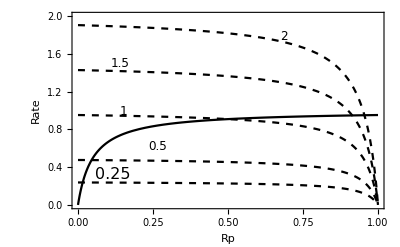

```mathematica
b1=Solve[sys2[[1]][[2]]==0/.parm,Rp[t]];(*nullclines*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

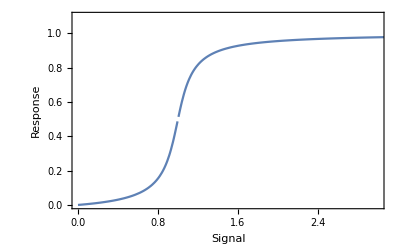

```mathematica
p1=Plot[Evaluate[{Rp[t]/.b1[[2]]}],{S,0,15},PlotRange->{{0,3},{0,1.1}},PlotRangeClipping->True,Frame->True,FrameLabel->{"Signal","Response"},LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
G[u_,v_,J_,K_]:= (2 u K)/(v-u +v J +u K+√((v-u+v J+u K)^2-4(v-u)u  K))(*Goldbeter-Koshland*)
```

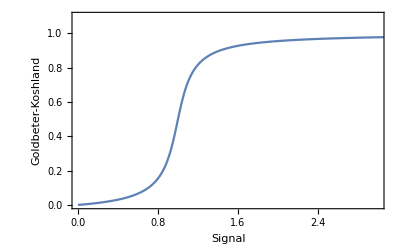

```mathematica
Plot[G[k1 S,k2,Km1/RT,Km2/RT]/.parm,{S,0,15},PlotRange->{{0,3},{0,1.1}},PlotRangeClipping->True,Frame->True,FrameLabel->{"Signal","Goldbeter-Koshland"},LabelStyle->{GrayLevel[0],Bold}]
```